# PolygonAngle function issue

There are some cases in which the default definition of the PolygonAngle function is not working, and instead of bringing the “Interior” values of a triangle, it brings the “FullExterior” values. And, for these same triangles, when using the function with the specification “FullExterior”, it returns the values that should be returned for the “Interior” specification.

```mathematica
??PolygonAngle
```

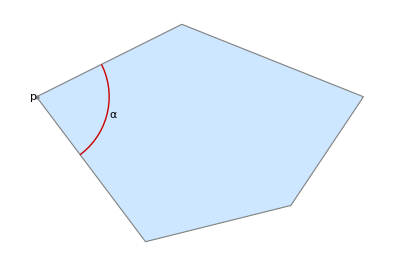
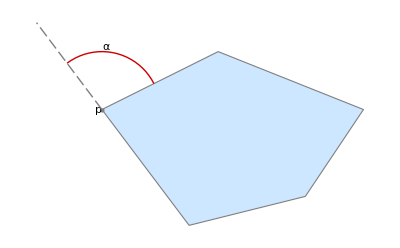
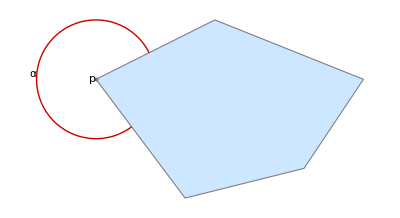
-Graphics- | -Graphics- | -Graphics-
"Interior" | "Exterior" | "FullExterior"

```mathematica
randomTriangles=Polygon/@RandomReal[{-100,100},{100,3,2}];
```

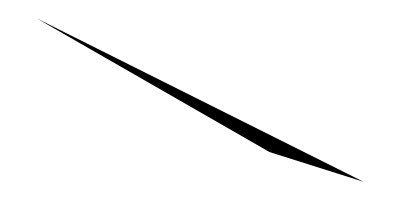
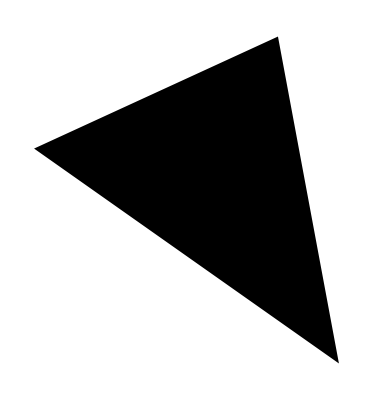
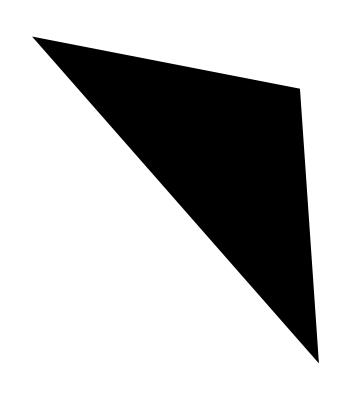
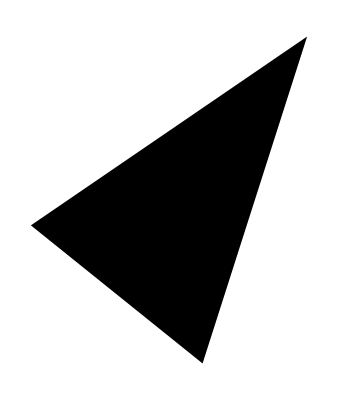
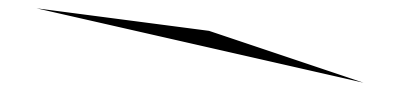
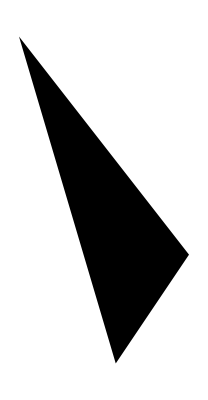
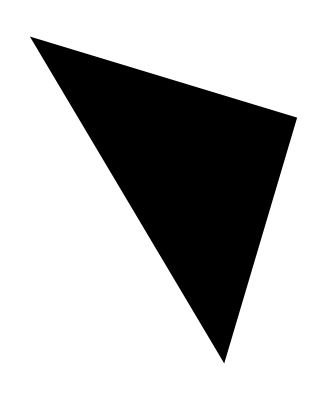
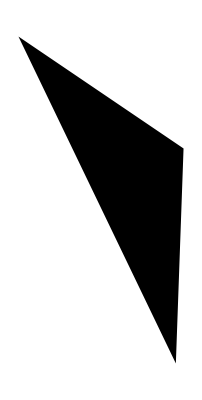

```mathematica
Row[Graphics/@randomTriangles⟦RandomInteger[100,10]⟧]
```

```mathematica
N@*Total@PolygonAngle@#&/@randomTriangles
```

{3.14159,3.14159,15.708,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,15.708,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,15.708,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,15.708,15.708,3.14159,3.14159,15.708,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,15.708,15.708,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,15.708,15.708,15.708,3.14159,3.14159,15.708,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,15.708,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,15.708,3.14159,3.14159,3.14159,3.14159,15.708,3.14159,3.14159,15.708,3.14159,3.14159,15.708,3.14159,3.14159}

```mathematica
N@Pi
```

3.14159

```mathematica
rightResult=Select[randomTriangles,N[Total[PolygonAngle@#]]==N@Pi&];
rightResult//Length
```

83

```mathematica
wrongResult=Select[randomTriangles,N[Total[PolygonAngle@#]]!=N@Pi&];
wrongResult//Length
```

17

```mathematica
N[Total@PolygonAngle[#,"FullExterior"]]==N@Pi&/@wrongResult
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

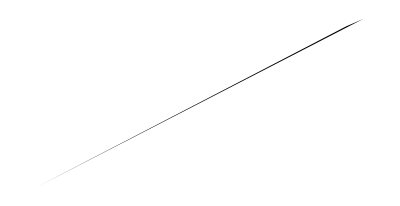
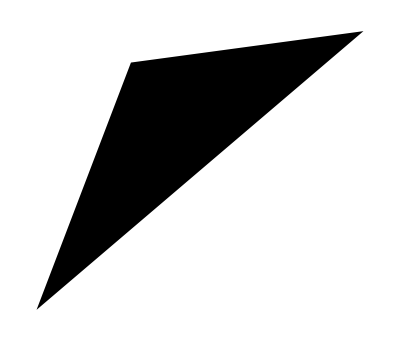
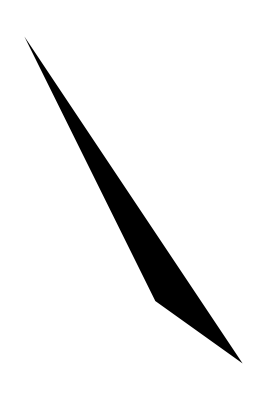
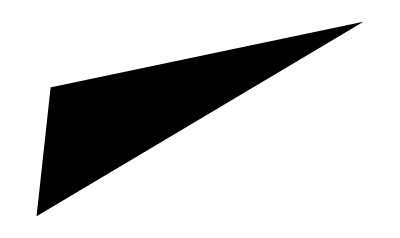
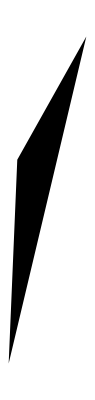
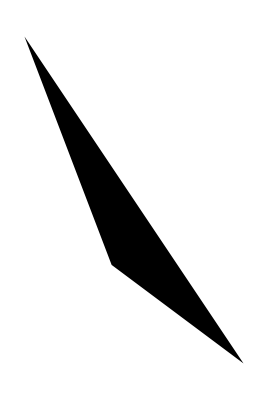
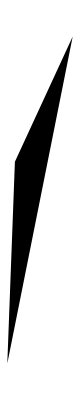
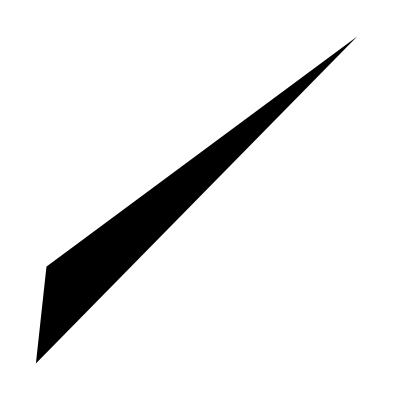
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[Graphics/@wrongResult]
```

```mathematica
(*Shoing the angles for each tested triangle, separted by right and wrong cases.*)
{TableForm[N[#/Degree]&/@PolygonAngle[#]&/@rightResult],TableForm[N[#/Degree]&/@PolygonAngle[#,"FullExterior"]&/@wrongResult]}
```

{24.873 | 34.2986 | 120.828
74.9038 | 28.7607 | 76.3355
29.3893 | 86.7592 | 63.8516
73.104 | 68.9738 | 37.9222
30.1669 | 27.8259 | 122.007
97.4283 | 58.339 | 24.2327
85.9622 | 33.8783 | 60.1595
23.8 | 77.5438 | 78.6562
72.5919 | 22.71 | 84.6982
60.6663 | 95.6354 | 23.6983
33.6244 | 122.654 | 23.7218
52.3885 | 41.2919 | 86.3196
50.3017 | 49.9663 | 79.732
16.9508 | 108.924 | 54.125
63.5131 | 106.018 | 10.469
133.755 | 25.0203 | 21.2243
80.3372 | 51.4248 | 48.238
11.1526 | 35.8748 | 132.973
5.41868 | 5.78249 | 168.799
104.022 | 60.6859 | 15.2921
4.31452 | 0.527364 | 175.158
84.7865 | 22.572 | 72.6414
48.7035 | 89.1276 | 42.1689
38.1043 | 97.7379 | 44.1578
28.6348 | 69.3282 | 82.037
36.8536 | 59.132 | 84.0144
4.83733 | 151.211 | 23.9518
24.34 | 109.794 | 45.8661
91.3113 | 39.6994 | 48.9893
63.6327 | 58.868 | 57.4992
48.8527 | 45.1464 | 86.0009
8.07867 | 29.9542 | 141.967
7.53558 | 10.9465 | 161.518
45.9461 | 45.4023 | 88.6515
59.8143 | 44.2698 | 75.9159
20.1238 | 34.8111 | 125.065
22.9762 | 124.504 | 32.5194
38.1489 | 61.4559 | 80.3952
66.1084 | 11.123 | 102.769
89.9308 | 54.0225 | 36.0468
33.1958 | 33.1196 | 113.685
159.614 | 9.09438 | 11.2916
2.99968 | 37.9503 | 139.05
65.3132 | 85.9137 | 28.7731
122.088 | 8.98711 | 48.925
10.3009 | 53.6972 | 116.002
52.5482 | 91.2624 | 36.1894
22.462 | 37.9854 | 119.553
17.6936 | 81.2336 | 81.0728
32.8657 | 23.7051 | 123.429
33.9094 | 41.6785 | 104.412
37.7038 | 37.3306 | 104.966
6.09753 | 159.394 | 14.5089
18.7531 | 0.760253 | 160.487
52.6027 | 101.2 | 26.1968
0.0901179 | 0.145354 | 179.765
32.5799 | 63.8855 | 83.5346
147.022 | 5.58805 | 27.3904
0.638583 | 1.17687 | 178.185
33.9653 | 54.0754 | 91.9593
1.36829 | 1.55367 | 177.078
72.8438 | 86.4603 | 20.6959
95.469 | 15.9219 | 68.6091
90.2475 | 53.21 | 36.5425
22.6876 | 98.6678 | 58.6446
34.1014 | 32.6256 | 113.273
56.9647 | 46.9621 | 76.0732
74.9662 | 39.7578 | 65.276
11.9451 | 124.287 | 43.7677
11.5223 | 72.1827 | 96.295
42.3736 | 47.3341 | 90.2923
23.367 | 48.1266 | 108.506
21.4744 | 50.5247 | 108.001
33.2602 | 35.4203 | 111.32
14.4545 | 128.111 | 37.4347
33.3502 | 58.8762 | 87.7735
37.8956 | 63.0902 | 79.0142
90.9484 | 64.4987 | 24.5528
8.86038 | 164.484 | 6.65556
60.4435 | 54.3653 | 65.1911
64.7962 | 85.1315 | 30.0723
144.226 | 31.9473 | 3.82711
54.3407 | 53.8118 | 71.8475,0.197938 | 176.152 | 3.64971
28.6342 | 118.556 | 32.8099
7.38902 | 20.7075 | 151.903
47.1134 | 13.0729 | 119.814
53.0025 | 108.09 | 18.9074
11.0501 | 152.923 | 16.0272
12.9544 | 19.4138 | 147.632
3.29383 | 9.01902 | 167.687
8.01481 | 159.953 | 12.0324
38.2712 | 132.748 | 8.98076
16.3723 | 45.525 | 118.103
24.4427 | 113.795 | 41.7627
12.4113 | 140.239 | 27.3493
11.7517 | 134.404 | 33.8441
50.7801 | 117.988 | 11.232
21.45 | 134.205 | 24.3451
16.9982 | 2.52333 | 160.478}

```mathematica
PolygonAngle[First@wrongResult,#]&/@First@First@wrongResult
PolygonAngle[First@wrongResult,#,"FullExterior"]&/@First@First@wrongResult
```

{6.27973,3.20875,6.21949}

{0.00345467,3.07444,0.0636994}

## Environment in which the error was found